# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Entropy\\Prethermalization\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Entanglement

```mathematica
(*2. Parameters*)
L=6;
J=1;
g=2.;
hlist=Sort[Append[Table[10^i,{i,-6,-1,0.5}],0.0]];
tlist=Developer`ToPackedArray[Table[10^i,{i,-1,10,0.0050}]];
tlist//Length
hlist//Length
```

2201

12

```mathematica
states=Table[RandomChainProductState[L],{10}];
```

```mathematica
states=Table[Flatten[KroneckerProduct[haar[L/2],haar[L/2]]],{100}];
```

```mathematica
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

```mathematica
(*3. Build block maps and compiled fast expander*)
{evenMap,oddMap}=buildMaps[L];
ExpandFullStateFast=buildExpandFullStateFast[evenMap,oddMap,L];
```

```mathematica
(*4. Hamiltonian and evolvers*)
h=hlist[[-1]];
Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddEigvals,oddEigvecs}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*5. Distribute*)
DistributeDefinitions[evenMap,oddMap,ProjectBlockVector,ExpandFullStateFast,tlist,L,new,evenEvolver,oddEvolver];
```

```mathematica
(*6. Define worker on all kernels*)
ParallelEvaluate[entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];];
```

```mathematica
(*7. Run computation*)
AbsoluteTiming[data=ParallelTable[entanglementWorker[state],{state,states}];]
```

{0.355555,Null}

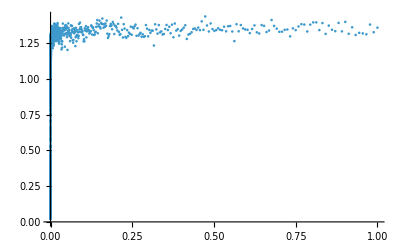

```mathematica
ListPlot[Transpose[{tlist,Mean[data]}],PlotRange->All]
```

## Exporting files

```mathematica
(* ===0) OUTPUT FOLDER+HELPERS (add this BEFORE the Do loop)===*)
outDir=FileNameJoin[{NotebookDirectory[],"SRN_entropies"}];
If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];
(*file-safe tag for h values,e.g.0.001->"h_0p001"*)
hTag[h_?NumericQ]:="h_"<>StringReplace[ToString@NumberForm[h,{Infinity,10}],{"."->"p","-"->"m"," "->""}];
(*metadata to write once at the end*)
runMeta=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"tlist"->tlist,"NumStates"->Length[states],"TimestampStart"->DateString[{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}],"WolframVersion"->$Version|>;
(*optional:keep a small per-h timing log*)
perHLog=Association[];
(*safe numeric tag for g (unchanged if you already added it)*)
gTag[x_?NumericQ]:=Module[{d=IntegerString[Floor[FractionalPart[x]*10^4+0.5],10,4]},"1p"<>d];
(*filename base using the INDEX ih,zero-padded to 2 digits*)
baseNameIdx[ih_Integer?Positive]:=StringJoin["SRN_entropies_","L",ToString[L],"_","J",ToString[J],"_","g",gTag[g],"_","h_",IntegerString[ih,10,2]  (*i01,i02,...*)];
```

```mathematica
results={};
Do[
Print["Computing for h = "<>ToString[hlist[[ih]]]];
h=hlist[[ih]];
(*Your step 4:Hamiltonian and evolvers (UNCHANGED)*)Ha=IsingHamiltonian[h,g,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha,Symmetry->"Parity"];
{evenEigvals,evenEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[1]]];
{oddEigvals,oddEigvecs}=Transpose@Sort@Transpose@Quiet@Eigensystem[system[[2]]];
evenEigvecs=Developer`ToPackedArray[evenEigvecs];
evenEigvals=Developer`ToPackedArray[evenEigvals];
oddEigvecs=Developer`ToPackedArray[oddEigvecs];
oddEigvals=Developer`ToPackedArray[oddEigvals];
evenEvolver=compiledEvolverSector[evenEigvecs,evenEigvals];
oddEvolver=compiledEvolverSector[oddEigvecs,oddEigvals];
(*Local (non-parallel) worker using the evolvers for THIS h—UNCHANGED*)entanglementWorker[state_]:=Module[{psiEven,psiOdd,evenFinal,oddFinal,fullStates},{psiEven,psiOdd}={ProjectBlockVector[state,evenMap,"even",L],ProjectBlockVector[state,oddMap,"odd",L]};
evenFinal=evenEvolver[psiEven,tlist];
oddFinal=oddEvolver[psiOdd,tlist];
fullStates=Table[ExpandFullStateFast[evenFinal[[i]],oddFinal[[i]]],{i,Length[tlist]}];
Map[new[#,L]&,fullStates]];
(* ===Only addition:time+export per h===*)
{dt,currentResults}=AbsoluteTiming[ParallelTable[entanglementWorker[state],{state,states}]];
AppendTo[results,currentResults];
perHLog[h]=<|"Seconds"->dt,"ResultShape"->Dimensions[currentResults]|>;
(*build trajectories:one {t,S(t)} table per state*)
trajectories=Map[Transpose[{tlist,#}]&,currentResults];
Export[FileNameJoin[{outDir,baseNameIdx[ih]<>".mx"}],trajectories,"MX"];

,{ih,Length[hlist]}];

(* ===Write metadata once at the end===*)
runMetaFinal=<|"L"->L,"J"->J,"g"->g,"hlist"->hlist,"NumStates"->Length[states],"PerHFiles"->AssociationThread[hlist,Table[baseNameIdx[i]<>".mx",{i,Length[hlist]}]]|>;
metadata=runMetaFinal;
Put[metadata,FileNameJoin[{outDir,"metadata.m"}]];
Print["Saved per-h .mx files and metadata.m to: ",outDir];
```

Computing for h = 0.

Computing for h =      -6
1. 10

Computing for h =           -6
3.16228 10

Computing for h = 0.00001

Computing for h = 0.0000316228

Computing for h = 0.0001

Computing for h = 0.000316228

Computing for h = 0.001

Computing for h = 0.00316228

Computing for h = 0.01

Computing for h = 0.0316228

Computing for h = 0.1

Saved per-h .mx files and metadata.m to: C:\Users\Miguel\Github\Entropy\Prethermalization\Late time ensembles\SRN_entropies

```mathematica
data=results;
```

```mathematica
plotsa={};
Do[
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[data[[h]]]}],MovingAverage[Transpose[{tlist,Mean[data[[h]]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.30]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["SRN, OBC, Half Haar , L = "<>ToString[L]<>", J = "<>ToString[N[J]]<>", g = "<>ToString[N[g]]<>", h = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plotsa,ploten];
,{h,Length[hlist]}];
```

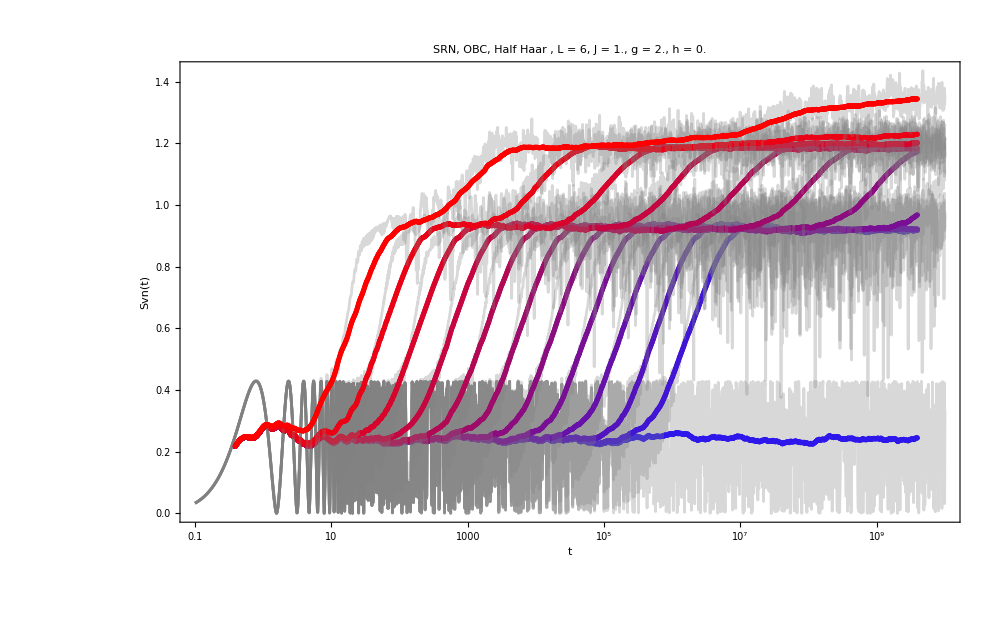

```mathematica
Show[plotsa,PlotRange->All]
```

# Husimi as entanglement measaure

```mathematica
(*Clear previous definitions to ensure a clean slate*)
ClearAll["Global`*"];
(*1. Basic Pauli Matrices*)
Id=IdentityMatrix[2];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3];
(*2. Tensor Product Construction mkKron[op,site,N] creates an operator acting as'op' on'site' and Identity on all others in a chain of length Nsys.*)
mkKron[op_,site_,Nsys_]:=Module[{list},list=ConstantArray[Id,Nsys];
list[[site]]=op;
KroneckerProduct@@list];
```

```mathematica
(*3. Helper to build the full Many-Body Hamiltonian Mixed Field Ising Model (Open Boundary Conditions) H=-J Sum(Z_i Z_{i+1})-hx Sum(X_i)-hz Sum(Z_i)*)
createHamiltonian[Nsys_,J_,hx_,hz_]:=Module[{H},
(*Interaction Term*)H=-J*Sum[mkKron[sz,i,Nsys].mkKron[sz,i+1,Nsys],{i,1,Nsys-1}];
(*Transverse Field*)H=H-hx*Sum[mkKron[sx,i,Nsys],{i,1,Nsys}];
(*Longitudinal Field*)H=H-hz*Sum[mkKron[sz,i,Nsys],{i,1,Nsys}];
Return[H];];
```

```mathematica
(*Parameters*)
Nsys=4;
Jval=1.0;
hxVal=0.5;
hzVal=0.3;
time=10.0; 

(*Generate Hamiltonian*)
Ham=createHamiltonian[Nsys,Jval,hxVal,hzVal];
```

```mathematica
Ham//Dimensions
```

{16,16}

```mathematica
(*Create Initial Random Product State|psi(0)>We generate random theta/phi for each spin to ensure zero entanglement initially.*)
randomQubit[]:=Module[{theta,phi},theta=RandomReal[{0,Pi}];
phi=RandomReal[{0,2 Pi}];
{Cos[theta/2],Exp[I phi] Sin[theta/2]}];
psi0=Flatten[KroneckerProduct@@Table[randomQubit[],{Nsys}]];
```

```mathematica
psi0//Dimensions
```

{16}

```mathematica
(*Time Evolution Operator U=Exp[-i H t]*)
U=MatrixExp[-I*Ham*time];
```

```mathematica
U//Dimensions
```

{16,16}

```mathematica
(*Evolved State|psi(t)>*)
psit=U.psi0;
```

```mathematica
(*Check Normalization*)
Print["Norm of state: ",Norm[psit]];
```

Norm of state: 1.

```mathematica
(*1. Compact Definition of the Tool*)getPurityByReshuffling[stateVec_,keepSites_,nSys_]:=Module[{permOrder,stateTensor,dimKeep,dimTrace,rhoPermuted,rhoReduced},
If[Length[keepSites]==0||Length[keepSites]==nSys,Return[1]];
permOrder=Join[keepSites,Complement[Range[nSys],keepSites]];
stateTensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
(*Permute:Target system to the'left',Environment to the'right'*)
rhoPermuted=Dyad[Flatten[Transpose[stateTensor,permOrder]]];
dimKeep=2^Length[keepSites];
dimTrace=2^(nSys-Length[keepSites]);
rhoReduced=MatrixPartialTrace[rhoPermuted,2,{dimKeep,dimTrace}];
Chop[Tr[rhoReduced.rhoReduced]] ];
```

```mathematica
(*2. Define Test States (N=4)*)
basis[n_,val_]:=IntegerDigits[val,2,n];
ket[n_,val_]:=Normal[SparseArray[{val+1}->1,2^n]]; 
(*A.Product State|0000>*)
psiProd=ket[4,0];
(*B.Bell Pairs|Phi+>_12 (x)|Phi+>_34*)
bellPair=Flatten[KroneckerProduct[{1,0,0,1},{1,0,0,1}]]/2;
(*C.GHZ State (|0000>+ |1111>)/Sqrt[2]*)
psiGHZ=(ket[4,0]+ket[4,15])/Sqrt[2];
(*D.W State (Dicke k=1):(|1000>+|0100>+|0010>+|0001>)/2*)
psiW=Total[Table[ket[4,2^i],{i,0,3}]]/2;
(*E.Haar Random State*)
psiHaar=Normalize[RandomComplex[{-1-I,1+I},16]];
```

```mathematica
(*3. Run Validation*)
states={{"Product",psiProd},{"Bell (12)(34)",bellPair},{"GHZ",psiGHZ},{"W-State",psiW},{"Haar Random",psiHaar}};
allSubsets=Subsets[Range[4]];
```

```mathematica
Print["N=4 System. Testing Purity Sums..."];
Print["-------------------------------------------------------------"];
Print["State","\t\t","Sum Purity","\t","Check (Subset {1})"];

Do[{label,psi}=item;
totalSum=0;
puritySub1=0;
Do[p=getPurityByReshuffling[psi,subset,4];
totalSum+=p;
If[subset=={1},puritySub1=p];,{subset,allSubsets}];
Print[label,"\t",NumberForm[totalSum,{5,2}],"\t\t",NumberForm[puritySub1,{4,3}]];,{item,states}];
```

N=4 System. Testing Purity Sums...

-------------------------------------------------------------

State		Sum Purity	Check (Subset {1})

Product	16		1

Bell (12)(34)	9		1/2

GHZ	9		1/2

W-State	10		5/8

Haar Random	8.89		0.510

```mathematica
(*1. Single Qubit Coherent State|theta,phi>*)(*Returns a list of 2 complex numbers*)
spinCoherent[theta_,phi_]:={Cos[theta/2],Exp[I*phi]*Sin[theta/2]};
getCoherentState[angles_List]:=Module[{nSys,singleStates},
nSys=Length[angles]/2;
singleStates=Table[spinCoherent[angles[[2*i-1]],angles[[2*i]]],{i,1,nSys}];
Flatten[KroneckerProduct@@singleStates]];
```

```mathematica
(*TEST:Check dimensions for N=4*)
testAngles=ConstantArray[0.0,2*4]; (*All zero angles*)
testState=getCoherentState[testAngles];
Print["Test Coherent State Dimensions (Expect 16): ",Dimensions[testState]];
Print["Norm (Expect 1.0): ",Norm[testState]];
```

Test Coherent State Dimensions (Expect 16): {16}

Norm (Expect 1.0): 1.

```mathematica
getHusimiValue[stateVec_,angles_List]:=Module[{braOmega,overlap},
(*Construct|Omega>*)
braOmega=getCoherentState[angles];
(*Compute Overlap<Omega|psi>*)(*Note:Conjugate[braOmega].stateVec is the standard dot product*)
overlap=Conjugate[braOmega].stateVec;
(*Return squared magnitude*)
Abs[overlap]^2];
```

```mathematica
(*TEST:Evaluate Q for psiProd (|0000>) at angles 0 (North Pole)*)
(*Expectation:Overlap should be 1.0*)
val=getHusimiValue[psiProd,ConstantArray[0.0,8]];
Print["Husimi Value for |0000> at North Pole (Expect 1.0): ",val];
```

Husimi Value for |0000> at North Pole (Expect 1.0): 1.

```mathematica
(*TEST:Evaluate Q for psiProd at Pi (South Pole)*)
(*Expectation:Overlap should be 0.0*)
val2=getHusimiValue[psiProd,ConstantArray[Pi,8]];
Print["Husimi Value for |0000> at South Pole (Expect 0.0): ",val2];
```

Husimi Value for |0000> at South Pole (Expect 0.0): 0

```mathematica
computeHusimiIntegral[stateVec_]:=Module[{Nsys,integrand,vars,limits},
Nsys=Log[2,Length[stateVec]];
(*1. Define symbolic variables for N spins*)
vars=Table[Unique["a"],{2*Nsys}];
(*2. Define Integration Limits*)(*Pairs of {0,Pi} for theta,{0,2Pi} for phi*)
limits=Flatten[Table[{{0,Pi},{0,2 Pi}},{i,1,Nsys}],1];
(*3. Define the Scalar Integrand Function*)
integrand=Function[a,Module[{val,measure},
val=getHusimiValue[stateVec,a];
(*The Measure:Product of Sin(theta_i)*)
measure=Product[Sin[a[[2*i-1]]],{i,1,Nsys}];
val^2*measure]];
(*4. Perform Monte Carlo Integration*)(*We inject the variables and limits into NIntegrate*)NIntegrate[integrand[vars],Evaluate[Sequence@@MapThread[Prepend,{limits,vars}]],Method->"MonteCarlo",MaxPoints->50000,PrecisionGoal->2,AccuracyGoal->2]];
```

```mathematica
(*RUN THE TEST*)
Print["Computing Integral for Evolved State (psit)..."];
integralResult=computeHusimiIntegral[psit];

Print["---------------------------------------"];
Print["Raw Integral Result: ",integralResult];
Print["---------------------------------------"];
```

Computing Integral for Evolved State (psit)...

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 224.269+0. ⅈ and 3.59948 for the integral and error estimates.

---------------------------------------

Raw Integral Result: 224.269

---------------------------------------

```mathematica
(*1. The Theoretical Geometric Factor for N=4 spins*)(*Factor is (2 Pi/3)^N*)
magicFactor=(2*Pi/3)^Nsys;
(*2. Compare LHS and RHS*)
(*Recall'sumPurities' from Step 2 and'integralResult' from Step 3*)
Print["--- Verification of the Exact Relation ---"];
Print["1. Sum of Purities (from Step 2):  ",sumPurities];
Print["2. Raw Husimi Integral (from Step 3): ",integralResult];
Print["3. Predicted Integral (Sum * Factor): ",sumPurities*magicFactor];
Print["4. Actual Integral:                   ",integralResult];
Print["Percentage Difference: ",Abs[(integralResult-(sumPurities*magicFactor))/integralResult]*100,"%"];
```

--- Verification of the Exact Relation ---

1. Sum of Purities (from Step 2):  11.7785

2. Raw Husimi Integral (from Step 3): 224.269

3. Predicted Integral (Sum * Factor): 226.633

4. Actual Integral:                   224.269

Percentage Difference: 1.05378%

```mathematica
(*1. Re-define Test States (for independence)*)
basis[n_,val_]:=IntegerDigits[val,2,n];
ket[n_,val_]:=Normal[SparseArray[{val+1}->1,2^n]];
psiProd=ket[4,0];
psiBell=Flatten[KroneckerProduct[{1,0,0,1},{1,0,0,1}]]/2;
psiGHZ=(ket[4,0]+ket[4,15])/Sqrt[2];
psiW=Total[Table[ket[4,2^i],{i,0,3}]]/2;
testStates={{"Product (Separable)",psiProd},{"Bell Pairs (Local Ent)",psiBell},{"GHZ (Global Ent)",psiGHZ},{"W-State (Robust Ent)",psiW}};
(*2. Define the Magic Factor*)
(*The relation is:Integral=SumPurity*(2 Pi/3)^N*)
magicFactor=(2*Pi/3)^4;
```

```mathematica
(*3. Validation Loop*)
Print["Validating Exact Relation for N=4..."];
Print["Geometric Factor (2Pi/3)^4 = ",NumberForm[magicFactor,{5,2}]];
Print["----------------------------------------------------------------------------------"];
Print["State Name","\t\t","Sum Purity","\t","Predicted Int","\t","Actual Integral","\t","Error (%)"];
Print["----------------------------------------------------------------------------------"];
```

Validating Exact Relation for N=4...

Geometric Factor (2Pi/3)^4 = (16 π^4)/81

----------------------------------------------------------------------------------

State Name		Sum Purity	Predicted Int	Actual Integral	Error (%)

----------------------------------------------------------------------------------

```mathematica
Do[{label,state}=item;
(*A.Calculate Sum of Purities (Exact)*)
sumP=0;
Do[sumP+=getPurityByReshuffling[state,sub,4],{sub,Subsets[Range[4]]}];
(*B.Calculate Husimi Integral (Monte Carlo)*)(*Note:Using slightly fewer points (20k) for speed in this batch test*)
integralVal=computeHusimiIntegral[state];
(*C.Compare*)
predicted=sumP*magicFactor;
error=Abs[integralVal-predicted]/predicted*100;
Print[label,"\t",NumberForm[sumP,{4,1}],"\t\t",NumberForm[predicted,{5,1}],"\t\t",NumberForm[integralVal,{5,1}],"\t\t",NumberForm[error,{3,1}],"%"];,{item,testStates}];
```

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 303.138 and 4.28302 for the integral and error estimates.

Product (Separable)	16		(256 π^4)/81		303.1		1.5%

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 174.876+0. ⅈ and 2.04214 for the integral and error estimates.

Bell Pairs (Local Ent)	9		(16 π^4)/9		174.9		1.0%

GHZ (Global Ent)	9		(16 π^4)/9		170.7		1.5%

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 190.104+0. ⅈ and 2.5428 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

W-State (Robust Ent)	10		(160 π^4)/81		190.1		1.2%

```mathematica
(*1. Define Helper Functions (Compact Versions)*)(*Purity Sum*)getPuritySum[stateVec_,nSys_]:=Module[{sumP=0,sub,rhoFull},(*Optimized:Use explicit SVD for speed if N is small,or Reshuffle*)Do[sumP+=getPurityByReshuffling[stateVec,sub,nSys],{sub,Subsets[Range[nSys]]}];
sumP];

(*Husimi Integral (Monte Carlo)*)
(*Note:We reduce precision slightly for N>4 to keep it fast*)
getHusimiIntegral[stateVec_,nSys_]:=Module[{vars,limits,integrand},vars=Table[Unique["a"],{2*nSys}];
limits=Flatten[Table[{{0,Pi},{0,2 Pi}},{i,1,nSys}],1];
integrand=Function[a,getHusimiValue[stateVec,a]^2*Product[Sin[a[[2*i-1]]],{i,1,nSys}]];
NIntegrate[integrand[vars],Evaluate[Sequence@@MapThread[Prepend,{limits,vars}]],Method->"MonteCarlo",MaxPoints->If[nSys>=5,200000,50000],PrecisionGoal->2]];
```

```mathematica
(*2. Main Data Generation Loop*)
nValues={2,3,4,5}; (*We can try 6,but integration takes time*)
results={};

Print["Running Entropy Scaling Test (N = 2 to 5)..."];
Print["Target Bounds: ln(3Pi) ~ 2.24, ln(4Pi) ~ 2.53"];
Print["--------------------------------------------------------------------------------"];
Print["N  | State   | SumPurity Method | Integral Method | Theory Bound"];
Print["--------------------------------------------------------------------------------"];
```

Running Entropy Scaling Test (N = 2 to 5)...

Target Bounds: ln(3Pi) ~ 2.24, ln(4Pi) ~ 2.53

--------------------------------------------------------------------------------

N  | State   | SumPurity Method | Integral Method | Theory Bound

--------------------------------------------------------------------------------

```mathematica
Do[(*A.Generate States*)dim=2^n;
psiProd=Normal[SparseArray[{1}->1,dim]];(* |00...0>*)psiRand=Normalize[RandomComplex[{-1-I,1+I},dim]];
(*B.Product State Calculations*)valSumP=getPuritySum[psiProd,n];
(*Formula:S/N=Log[6Pi]-Log[SumP]/N*)sPurity=Log[6*Pi]-Log[valSumP]/n;
(*Integral for Product State is fast/exact,but let's MC it for consistency*)valInt=getHusimiIntegral[psiProd,n];
(*Formula:S/N=2Log[2Pi]-Log[Int]/N*)sInt=2*Log[2*Pi]-Log[valInt]/n;
Print[n,"  | Product | ",NumberForm[sPurity,{4,3}],"            | ",NumberForm[sInt,{4,3}],"           | ","2.243 (ln 3Pi)"];
AppendTo[results,{n,"Product",sPurity,sInt}];
(*C.Random State Calculations*)valSumP=getPuritySum[psiRand,n];
sPurity=Log[6*Pi]-Log[valSumP]/n;
valInt=getHusimiIntegral[psiRand,n];
sInt=2*Log[2*Pi]-Log[valInt]/n;
Print[n,"  | Random  | ",NumberForm[sPurity,{4,3}],"            | ",NumberForm[sInt,{4,3}],"           | ","2.531 (ln 4Pi)"];
AppendTo[results,{n,"Random",sPurity,sInt}];
Print["--------------------------------------------------------------------------------"];,{n,nValues}];
```

2  | Product | -Log[4]/2+Log[6 π]            | 2.245           | 2.243 (ln 3Pi)

2  | Random  | 2.258            | 2.256           | 2.531 (ln 4Pi)

--------------------------------------------------------------------------------

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 74.2917 and 0.744265 for the integral and error estimates.

3  | Product | -Log[8]/3+Log[6 π]            | 2.240           | 2.243 (ln 3Pi)

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 61.559+0. ⅈ and 0.821084 for the integral and error estimates.

3  | Random  | 2.294            | 2.302           | 2.531 (ln 4Pi)

--------------------------------------------------------------------------------

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 300.209 and 4.27486 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

4  | Product | -Log[16]/4+Log[6 π]            | 2.250           | 2.243 (ln 3Pi)

4  | Random  | 2.399            | 2.392           | 2.531 (ln 4Pi)

--------------------------------------------------------------------------------

5  | Product | -Log[32]/5+Log[6 π]            | 2.242           | 2.243 (ln 3Pi)

5  | Random  | 2.402            | 2.404           | 2.531 (ln 4Pi)

--------------------------------------------------------------------------------

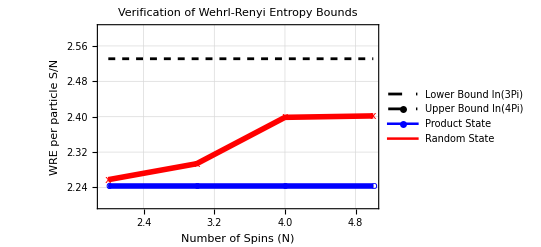

```mathematica
(*3. Visualization*)
ListLinePlot[{(*Theoretical Bounds*)Table[{n,Log[3*Pi]},{n,2,5}],Table[{n,Log[4*Pi]},{n,2,5}],(*Computed Data*)Select[results,#[[2]]=="Product"&][[All,{1,3}]],Select[results,#[[2]]=="Random"&][[All,{1,3}]]},PlotStyle->{{Dashed,Black},{Dashed,Black},(*Bounds*){Blue,Thickness[0.01]},(*Product State*){Red,Thickness[0.01]}            (*Random State*)},PlotMarkers->{None,None,"o","x"},PlotLegends->{"Lower Bound ln(3Pi)","Upper Bound ln(4Pi)","Product State","Random State"},Frame->True,FrameLabel->{"Number of Spins (N)","WRE per particle S/N"},GridLines->Automatic,PlotRange->{2.2,2.6},PlotLabel->"Verification of Wehrl-Renyi Entropy Bounds"]
```

```mathematica
(*---1. Compact Helper Functions---*)(*Purity Sum Calculation*)getPuritySum[stateVec_,nSys_]:=Module[{sumP=0,sub},Do[sumP+=getPurityByReshuffling[stateVec,sub,nSys],{sub,Subsets[Range[nSys]]}];
sumP];

(*Husimi Integral Calculation (Monte Carlo)*)
getHusimiIntegral[stateVec_,nSys_]:=Module[{vars,limits,integrand},vars=Table[Unique["a"],{2*nSys}];
limits=Flatten[Table[{{0,Pi},{0,2 Pi}},{i,1,nSys}],1];
integrand=Function[a,getHusimiValue[stateVec,a]^2*Product[Sin[a[[2*i-1]]],{i,1,nSys}]];
(*Lower precision slightly for speed on N=5*)NIntegrate[integrand[vars],Evaluate[Sequence@@MapThread[Prepend,{limits,vars}]],Method->"MonteCarlo",MaxPoints->If[nSys>=5,100000,50000],PrecisionGoal->2]];
```

================================================================================

VERIFYING WEHRL-RENYI ENTROPY BOUNDS

Lower Bound: ln(3Pi) ~ 2.243

Upper Bound: ln(4Pi) ~ 2.531

================================================================================

N  | State type  | From Purities | From Integral | Difference

--------------------------------------------------------------------------------

2  | Product     | -Log[4]/2+Log[6 π]         | 2.242         | 0.0016

2  | Haar Random | 2.250         | 2.248         | 0.0017

--------------------------------------------------------------------------------

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 73.9522 and 0.742004 for the integral and error estimates.

3  | Product     | -Log[8]/3+Log[6 π]         | 2.241         | 0.0021

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 52.4304+0. ⅈ and 0.548357 for the integral and error estimates.

3  | Haar Random | 2.330         | 2.356         | 0.0255

--------------------------------------------------------------------------------

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 315.238 and 4.41372 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

4  | Product     | -Log[16]/4+Log[6 π]         | 2.237         | 0.0059

4  | Haar Random | 2.369         | 2.369         | 0.0003

--------------------------------------------------------------------------------

5  | Product     | -Log[32]/5+Log[6 π]         | 2.245         | 0.0019

5  | Haar Random | 2.388         | 2.393         | 0.0049

--------------------------------------------------------------------------------

6  | Product     | -Log[64]/6+Log[6 π]         | 2.250         | 0.0070

6  | Haar Random | 2.421         | 2.423         | 0.0016

--------------------------------------------------------------------------------

7  | Product     | -Log[128]/7+Log[6 π]         | 2.244         | 0.0009

7  | Haar Random | 2.441         | 2.439         | 0.0020

--------------------------------------------------------------------------------

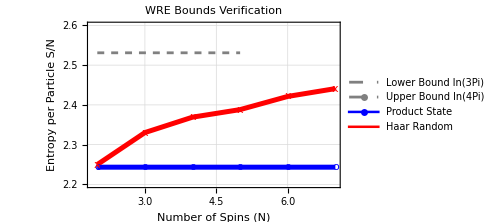

```mathematica
nValues={2,3,4,5,6,7};
results={};

Print["================================================================================"];
Print["VERIFYING WEHRL-RENYI ENTROPY BOUNDS"];
Print["Lower Bound: ln(3Pi) ~ 2.243"];
Print["Upper Bound: ln(4Pi) ~ 2.531"];
Print["================================================================================"];
Print["N  | State type  | From Purities | From Integral | Difference"];
Print["--------------------------------------------------------------------------------"];

Do[(*A.Generate States*)dim=2^n;
psiProd=Normal[SparseArray[{1}->1,dim]];(* |00...0>*)(*Haar Random State:Normalized vector of random complex numbers*)psiHaar=Normalize[RandomComplex[{-1-I,1+I},dim]];
(*---B.Product State Analysis---*)(*1. Purity Method*)sumP=getPuritySum[psiProd,n];
sPurity=Log[6*Pi]-Log[sumP]/n;
(*2. Integral Method*)intVal=getHusimiIntegral[psiProd,n];
sInt=2*Log[2*Pi]-Log[intVal]/n;
Print[n,"  | Product     | ",NumberForm[sPurity,{4,3}],"         | ",NumberForm[sInt,{4,3}],"         | ",NumberForm[Abs[sPurity-sInt],{4,4}]];
AppendTo[results,{n,"Product",sPurity}];
(*---C.Haar Random State Analysis---*)(*1. Purity Method*)sumP=getPuritySum[psiHaar,n];
sPurity=Log[6*Pi]-Log[sumP]/n;
(*2. Integral Method*)intVal=getHusimiIntegral[psiHaar,n];
sInt=2*Log[2*Pi]-Log[intVal]/n;
Print[n,"  | Haar Random | ",NumberForm[sPurity,{4,3}],"         | ",NumberForm[sInt,{4,3}],"         | ",NumberForm[Abs[sPurity-sInt],{4,4}]];
AppendTo[results,{n,"Haar",sPurity}];
Print["--------------------------------------------------------------------------------"];,{n,nValues}];


(*---3. Visualization---*)

ListLinePlot[{(*Theoretical Bounds*)Table[{n,Log[3*Pi]},{n,2,5}],Table[{n,Log[4*Pi]},{n,2,5}],(*Computed Data*)Select[results,#[[2]]=="Product"&][[All,{1,3}]],Select[results,#[[2]]=="Haar"&][[All,{1,3}]]},PlotStyle->{{Dashed,Gray},{Dashed,Gray},(*Bounds*){Blue,Thickness[0.01]},(*Product State*){Red,Thickness[0.01]}          (*Haar Random State*)},PlotMarkers->{None,None,"o","x"},PlotLegends->{"Lower Bound ln(3Pi)","Upper Bound ln(4Pi)","Product State","Haar Random"},Frame->True,FrameLabel->{"Number of Spins (N)","Entropy per Particle S/N"},GridLines->Automatic,PlotRange->{2.2,2.6},PlotLabel->"WRE Bounds Verification",ImageSize->Medium]
```

```mathematica
(*0. Clear previous definitions to prevent conflicts*)
ClearAll["Global`*"];
(*1. Define Core Functions Re-verifid*)
(*Coherent State|theta,phi>*)
spinCoherent[theta_,phi_]:={Cos[theta/2],Exp[I*phi]*Sin[theta/2]};
getCoherentState[angles_List]:=Flatten[KroneckerProduct@@Table[spinCoherent[angles[[2*i-1]],angles[[2*i]]],{i,1,Length[angles]/2}]];
(*Husimi Value Q= |<Omega|Psi>|^2*)
getHusimiValue[stateVec_,angles_List]:=Abs[Conjugate[getCoherentState[angles]].stateVec]^2;
(*Purity Calculation (Reshuffling)*)
getPurityByReshuffling[stateVec_,keepSites_,nSys_]:=Module[{permOrder,stateTensor,dimKeep,dimTrace,rhoPermuted,rhoReduced},If[Length[keepSites]==0||Length[keepSites]==nSys,Return[1]];
permOrder=Join[keepSites,Complement[Range[nSys],keepSites]];
stateTensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
rhoPermuted=Dyad[Flatten[Transpose[stateTensor,permOrder]]];
dimKeep=2^Length[keepSites];
dimTrace=2^(nSys-Length[keepSites]);
rhoReduced=MatrixPartialTrace[rhoPermuted,2,{dimKeep,dimTrace}];
Re[Tr[rhoReduced.rhoReduced]]];
getPuritySum[stateVec_,nSys_]:=Total[Table[getPurityByReshuffling[stateVec,sub,nSys],{sub,Subsets[Range[nSys]]}]];
```

```mathematica
getHusimiIntegral[stateVec_,nSys_]:=Module[{vars,limits,integrand},
vars=Table[Unique["a"],{2*nSys}];
limits=Flatten[Table[{{0,Pi},{0,2 Pi}},{i,1,nSys}],1];
integrand=Function[a,getHusimiValue[stateVec,a]^2*Product[Sin[a[[2*i-1]]],{i,1,nSys}]];
NIntegrate[integrand[vars],Evaluate[Sequence@@MapThread[Prepend,{limits,vars}]],Method->"MonteCarlo",MaxPoints->50000,PrecisionGoal->2]];
```

```mathematica
(*3. Main Loop N=2 to 8*)
Print["Starting Calculation (N=2 to 8)..."];
```

Starting Calculation (N=2 to 8)...

```mathematica
purityProduct={};purityHaar={};purityGHZ={};
intProduct={};intHaar={};intGHZ={};

Do[
(*A.Generate States*)
dim=2^n;
psiProd=Normal[SparseArray[{1}->1,dim]];(* |00...0>*)
psiHaar=Normalize[RandomComplex[{-1-I,1+I},dim]];
psiGHZ=Normal[SparseArray[{1->1,dim->1},dim]]/Sqrt[2];
(*Group them for easy looping.NOTE:Simple List of Lists.*)
statesList={{"Product",psiProd},{"Haar",psiHaar},{"GHZ",psiGHZ}};
(*B.Compute Purities (Fast)*)
Do[type=pair[[1]];
psi=pair[[2]];
sumP=getPuritySum[psi,n];
valS=Log[6*Pi]-Log[sumP]/n;
If[type=="Product",AppendTo[purityProduct,{n,valS}]];
If[type=="Haar",AppendTo[purityHaar,{n,valS}]];
If[type=="GHZ",AppendTo[purityGHZ,{n,valS}]];,{pair,statesList}];

(*C.Compute Integrals (Only up to N=5)*)
If[n<=8,Do[type=pair[[1]];
psi=pair[[2]];
rawInt=getHusimiIntegral[psi,n];
valS=2*Log[2*Pi]-Log[rawInt]/n;
If[type=="Product",AppendTo[intProduct,{n,valS}]];
If[type=="Haar",AppendTo[intHaar,{n,valS}]];
If[type=="GHZ",AppendTo[intGHZ,{n,valS}]];,{pair,statesList}];];
Print["Finished N = ",n];
,{n,2,8}];
```

Finished N = 2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 73.6921 and 0.739217 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 55.0796+0. ⅈ and 0.680481 for the integral and error estimates.

Finished N = 3

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 310.058 and 4.33607 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

Finished N = 4

Finished N = 5

Finished N = 6

Finished N = 7

Finished N = 8

```mathematica
(*4. Visualization*)
bounds={Table[{n,Log[3*Pi]},{n,2,8}],(*Lower*)Table[{n,Log[4*Pi]},{n,2,8}]  (*Upper*)};
```

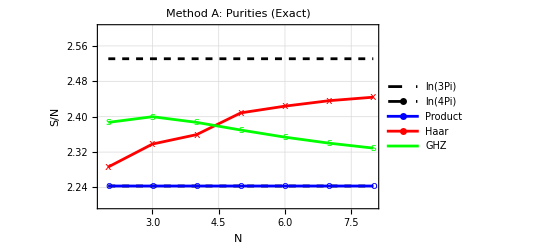

```mathematica
(*Plot 1:Purity Method*)
plot1=ListLinePlot[{bounds[[1]],bounds[[2]],purityProduct,purityHaar,purityGHZ},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},PlotRange->{2.2,2.6},Frame->True,GridLines->Automatic,FrameLabel->{"N","S/N"},PlotLabel->"Method A: Purities (Exact)",PlotLegends->{"ln(3Pi)","ln(4Pi)","Product","Haar","GHZ"}]
```

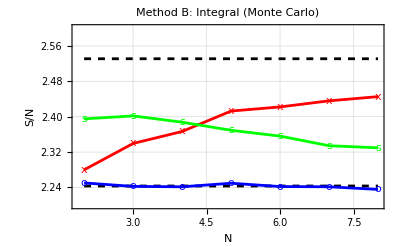

```mathematica
(*Plot 2:Integral Method*)
plot2=ListLinePlot[{bounds[[1]],bounds[[2]],intProduct,intHaar,intGHZ},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},PlotRange->{2.2,2.6},Frame->True,GridLines->Automatic,FrameLabel->{"N","S/N"},PlotLabel->"Method B: Integral (Monte Carlo)",PlotLegends->None]
```

## improvements

```mathematica
(*0. Clear Everything*)ClearAll["Global`*"];

(*---1. ROBUST PURITY FUNCTION (Using SVD)---*)
(*For a pure state,Purity(Reduced Rho)=Sum[SingularValues^4] of the reshaped state*)
getPuritySum[stateVec_,nSys_]:=Module[{dim,puritySum=0,sub,mat,sv},dim=2^nSys;
Do[(*1. Identify subsystem dimensions*)k=Length[sub];(*Size of subsystem A*)If[k==0||k==nSys,puritySum+=1,(*Purity of empty or full system is 1*)(*2. Reshape vector into Matrix (A vs Rest) for SVD*)(*We rely on the fact that Purity is invariant under permutation of the'Rest'*)(*We move the chosen sites to the front,then flatten*)(*Standard Mathematica reshuffle is tricky,so we use a simpler property:*)(*The sum of purities is sum of purities of all bipartitions.*)(*We will stick to the exact definition used previously but implemented simply:*)(*Re-implementing the robust reshuffle:*)perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
(*Transpose so'sub' indices are first*)tensorPerm=Transpose[tensor,perm];
(*Flatten into Matrix:(2^k) x (2^(N-k))*)mat=Flatten[tensorPerm,{{1},range=Range[2,nSys-k+1]+(k-1)}];
(*Actually ArrayReshape is safer here:*)mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
(*3. SVD Method:Purity=Sum(singular values^4)*)sv=SingularValueList[mat];
puritySum+=Total[sv^4];];,{sub,Subsets[Range[nSys]]}];
puritySum];


(*---2. INTEGRAL FUNCTIONS---*)
spinCoherent[theta_,phi_]:={Cos[theta/2],Exp[I*phi]*Sin[theta/2]};

getHusimiValue[stateVec_,angles_List]:=Module[{cohState},(*Construct coherent state on the fly*)cohState=Flatten[KroneckerProduct@@Table[spinCoherent[angles[[2*i-1]],angles[[2*i]]],{i,1,Length[angles]/2}]];
Abs[Conjugate[cohState].stateVec]^2];
```

```mathematica
getHusimiIntegral[stateVec_,nSys_]:=Module[{vars,limits,integrand},vars=Table[Unique["a"],{2*nSys}];
limits=Flatten[Table[{{0,Pi},{0,2 Pi}},{i,1,nSys}],1];
(*Compiled integrand for speed?No,symbolic is safer for NIntegrate here*)integrand=Function[a,getHusimiValue[stateVec,a]^2*Product[Sin[a[[2*i-1]]],{i,1,nSys}]];
(*Monte Carlo:Increased points slightly for higher N,strictly low precision*)NIntegrate[integrand[vars],Evaluate[Sequence@@MapThread[Prepend,{limits,vars}]],Method->"MonteCarlo",MaxPoints->50000,(*Fixed points to prevent hanging*)PrecisionGoal->1,AccuracyGoal->1 (*We accept noise for speed*)]];
```

```mathematica
(*---3. MAIN LOOP (N=2 to 8)---*)
(*Data Lists*)
purityData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;
integralData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;

Print["Starting Full Comparison (N=2 to 8)..."];
```

Starting Full Comparison (N=2 to 8)...

```mathematica
Do[(*1. Define States*)dim=2^n;
psiProd=Normal[SparseArray[{1}->1,dim]];
psiHaar=Normalize[RandomComplex[{-1-I,1+I},dim]];
psiGHZ=Normal[SparseArray[{1->1,dim->1},dim]]/Sqrt[2];
statesList={{"Product",psiProd},{"Haar",psiHaar},{"GHZ",psiGHZ}};
(*2. Compute Both Methods*)Do[{label,psi}=pair;
(*A.Purity Method*)valP=getPuritySum[psi,n];
sPurity=Log[6*Pi]-Log[valP]/n;
AppendTo[purityData[label],{n,sPurity}];
(*B.Integral Method (UNLOCKED)*)(*Warning:This line gets slower as n increases*)rawInt=getHusimiIntegral[psi,n];
sInt=2*Log[2*Pi]-Log[rawInt]/n;
AppendTo[integralData[label],{n,sInt}];,{pair,statesList}];
Print["Done N = ",n];,{n,2,8}];
```

Done N = 2

Done N = 3

Done N = 4

Done N = 5

Done N = 6

Done N = 7

Done N = 8

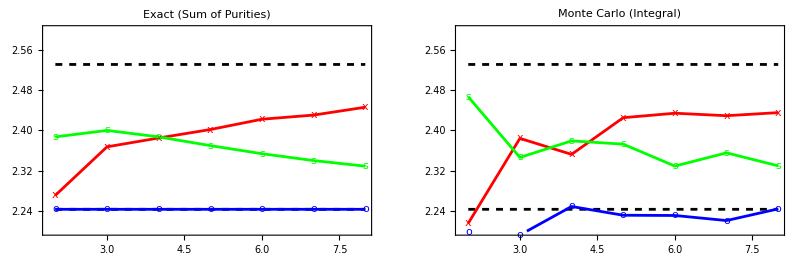

```mathematica
(*---4. VISUALIZATION---*)
bounds={Table[{n,Log[3*Pi]},{n,2,8}],Table[{n,Log[4*Pi]},{n,2,8}]};

plotPurity=ListLinePlot[{bounds[[1]],bounds[[2]],purityData["Product"],purityData["Haar"],purityData["GHZ"]},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},Frame->True,PlotRange->{2.2,2.6},ImageSize->400,PlotLabel->"Exact (Sum of Purities)"];

plotIntegral=ListLinePlot[{bounds[[1]],bounds[[2]],integralData["Product"],integralData["Haar"],integralData["GHZ"]},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},Frame->True,PlotRange->{2.2,2.6},ImageSize->400,PlotLabel->"Monte Carlo (Integral)"];

GraphicsRow[{plotPurity,plotIntegral},ImageSize->800]
```

```mathematica
randomPhaseSpacePoint[nSys_]:=Flatten[Table[{ArcCos[RandomReal[{-1,1}]],RandomReal[{0,2 Pi}]},{nSys}]];
(*PARALLELIZED MONTE CARLO INTEGRAL*)
getHusimiIntegral[stateVec_,nSys_]:=Module[{totalSamples=300000,batches,batchSize,volume=(4*Pi)^nSys },
(*1. Split work across available kernels*)
batches=Length[Kernels[]];
batchSize=Ceiling[totalSamples/batches];
(*2. Distribute the calculation*)(*Each kernel computes the average Q^2 over its batch of random points*)(*We sample theta via ArcCos uniform dist to handle Sin[theta] Jacobian naturally*)results=ParallelTable[Module[{sum=0.0,pt,val},
Do[(*Generate random point naturally weighted by Sin[theta]*)
pt=Flatten[Table[{ArcCos[RandomReal[{-1,1}]],RandomReal[{0,2 Pi}]},{nSys}]];
(*Calculate Q(alpha)*)val=getHusimiValue[stateVec,pt];
(*We integrate Q^2. Note:Jacobian is handled by point selection*)
sum+=val^2;,{batchSize}];
sum],{i,batches},DistributedContexts->Automatic];
(*3. Combine results*)(*Integral=Volume* <Average Value of Q^2>*)
(Total[results]/(batches*batchSize))*volume];
```

```mathematica
(*0. Clear Everything& Start Kernels*)
ClearAll["Global`*"];
If[Length[Kernels[]]==0,LaunchKernels[]];
(*---1. ROBUST PURITY FUNCTION (Using SVD)---*)
getPuritySum[stateVec_,nSys_]:=Module[{dim,puritySum=0,sub,mat,sv},dim=2^nSys;
Do[k=Length[sub];
If[k==0||k==nSys,puritySum+=1,perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
puritySum+=Total[sv^4];];,{sub,Subsets[Range[nSys]]}];
puritySum];
(*---2. OPTIMIZED PARALLEL INTEGRAL FUNCTIONS---*)
spinCoherent[theta_,phi_]:={Cos[theta/2],Exp[I*phi]*Sin[theta/2]};
getHusimiValue[stateVec_,angles_List]:=Module[{cohState},cohState=Flatten[KroneckerProduct@@Table[spinCoherent[angles[[2*i-1]],angles[[2*i]]],{i,1,Length[angles]/2}]];
Abs[Conjugate[cohState].stateVec]^2];
getHusimiIntegral[stateVec_,nSys_]:=Module[{totalSamples=280000,batches,batchSize,volume=(4*Pi)^nSys,results},batches=Length[Kernels[]];
If[batches==0,batches=1];(*Fallback if no kernels*)batchSize=Ceiling[totalSamples/batches];
results=ParallelTable[Module[{sum=0.0,pt,val},Do[(*Smart Sampling:accounts for Sin[theta] automatically*)pt=Flatten[Table[{ArcCos[RandomReal[{-1,1}]],RandomReal[{0,2 Pi}]},{nSys}]];
val=getHusimiValue[stateVec,pt];
sum+=val^2;,{batchSize}];
sum],{i,batches},DistributedContexts->Automatic];
(Total[results]/(batches*batchSize))*volume];
```

```mathematica
(*---3. MAIN LOOP (N=2 to 8)---*)
purityData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;
integralData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;
Print["Starting Calculation with Parallel Integration..."];
```

Starting Calculation with Parallel Integration...

```mathematica
Do[dim=2^n;
psiProd=Normal[SparseArray[{1}->1,dim]];
psiHaar=Normalize[RandomComplex[{-1-I,1+I},dim]];
psiGHZ=Normal[SparseArray[{1->1,dim->1},dim]]/Sqrt[2];
statesList={{"Product",psiProd},{"Haar",psiHaar},{"GHZ",psiGHZ}};
(*A.Purity Method*)
Do[{label,psi}=pair;
valP=getPuritySum[psi,n];
sPurity=Log[6*Pi]-Log[valP]/n;
AppendTo[purityData[label],{n,sPurity}];
,{pair,statesList}];

(*B.Integral Method (Now Parallelized)*)(*We can safely run this up to N=8 now*)
Do[{label,psi}=pair;
rawInt=getHusimiIntegral[psi,n];
sInt=2*Log[2*Pi]-Log[rawInt]/n;
AppendTo[integralData[label],{n,sInt}];,{pair,statesList}];
Print["Finished N = ",n];,{n,2,8}];
```

Finished N = 2

Finished N = 3

Finished N = 4

Finished N = 5

Finished N = 6

Finished N = 7

Finished N = 8

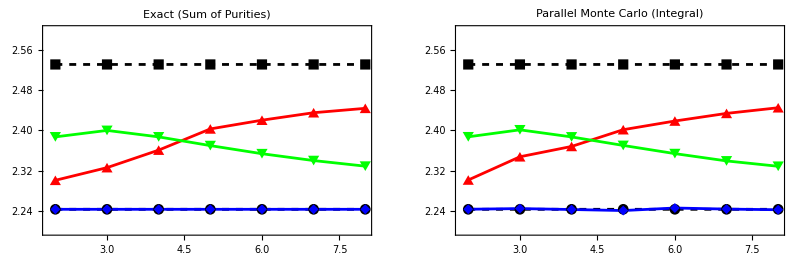

```mathematica
(*---4. VISUALIZATION---*)
bounds={Table[{n,Log[3*Pi]},{n,2,8}],Table[{n,Log[4*Pi]},{n,2,8}]};

plotPurity=ListPlot[{bounds[[1]],bounds[[2]],purityData["Product"],purityData["Haar"],purityData["GHZ"]},Joined->True,PlotMarkers->Automatic,PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},Frame->True,PlotRange->{2.2,2.6},ImageSize->400,PlotLabel->"Exact (Sum of Purities)"];

plotIntegral=ListPlot[{bounds[[1]],bounds[[2]],integralData["Product"],integralData["Haar"],integralData["GHZ"]},Joined->True,PlotMarkers->Automatic,PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},Frame->True,PlotRange->{2.2,2.6},ImageSize->400,PlotLabel->"Parallel Monte Carlo (Integral)"];

GraphicsRow[{plotPurity,plotIntegral},ImageSize->800]
```

```mathematica
(*0. Clear Everything& Start Kernels*)ClearAll["Global`*"];
If[Length[Kernels[]]==0,LaunchKernels[]];

(*---1. ROBUST PURITY FUNCTION (Using SVD)---*)
getPuritySum[stateVec_,nSys_]:=Module[{dim,puritySum=0,sub,mat,sv},dim=2^nSys;
Do[k=Length[sub];
If[k==0||k==nSys,puritySum+=1,perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
puritySum+=Total[sv^4];];,{sub,Subsets[Range[nSys]]}];
puritySum];

(*---2. OPTIMIZED PARALLEL INTEGRAL FUNCTIONS---*)
spinCoherent[theta_,phi_]:={Cos[theta/2],Exp[I*phi]*Sin[theta/2]};

getHusimiValue[stateVec_,angles_List]:=Module[{cohState},cohState=Flatten[KroneckerProduct@@Table[spinCoherent[angles[[2*i-1]],angles[[2*i]]],{i,1,Length[angles]/2}]];
Abs[Conjugate[cohState].stateVec]^2];

getHusimiIntegral[stateVec_,nSys_]:=Module[{totalSamples=200000,batches,batchSize,volume=(4*Pi)^nSys,results},batches=Length[Kernels[]];
If[batches==0,batches=1];
batchSize=Ceiling[totalSamples/batches];
results=ParallelTable[Module[{sum=0.0,pt,val},Do[(*Smart Sampling:accounts for Sin[theta] automatically*)pt=Flatten[Table[{ArcCos[RandomReal[{-1,1}]],RandomReal[{0,2 Pi}]},{nSys}]];
val=getHusimiValue[stateVec,pt];
sum+=val^2;,{batchSize}];
sum],{i,batches},DistributedContexts->Automatic];
(Total[results]/(batches*batchSize))*volume];
```

```mathematica
(*---3. MAIN LOOP (N=2 to 8) WITH ENSEMBLE AVERAGING---*)
purityData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;
integralData=<|"Product"->{},"Haar"->{},"GHZ"->{}|>;

ensembleSize=50; (*Number of random states to average*)

Print["Starting Calculation (Averaging over 50 Haar states)..."];
```

Starting Calculation (Averaging over 50 Haar states)...

```mathematica
Do[
dim=2^n;
(*---A.Deterministic States (Run Once)---*)
psiProd=Normal[SparseArray[{1}->1,dim]];
psiGHZ=Normal[SparseArray[{1->1,dim->1},dim]]/Sqrt[2];
(*Product*)AppendTo[purityData["Product"],{n,Log[6*Pi]-Log[getPuritySum[psiProd,n]]/n}];
AppendTo[integralData["Product"],{n,2*Log[2*Pi]-Log[getHusimiIntegral[psiProd,n]]/n}];
(*GHZ*)AppendTo[purityData["GHZ"],{n,Log[6*Pi]-Log[getPuritySum[psiGHZ,n]]/n}];
AppendTo[integralData["GHZ"],{n,2*Log[2*Pi]-Log[getHusimiIntegral[psiGHZ,n]]/n}];

(*---B.Haar Random Ensemble (Run 50 Times)---*)
sPuritySum=0.0;
sIntegralSum=0.0;
Do[psiRand=Normalize[RandomComplex[{-1-I,1+I},dim]];
(*Purity Entropy*)
valP=getPuritySum[psiRand,n];
sPuritySum+=(Log[6*Pi]-Log[valP]/n);
(*Integral Entropy*)
valI=getHusimiIntegral[psiRand,n];
sIntegralSum+=(2*Log[2*Pi]-Log[valI]/n);,{k,1,ensembleSize}];
(*Average and Store*)
AppendTo[purityData["Haar"],{n,sPuritySum/ensembleSize}];
AppendTo[integralData["Haar"],{n,sIntegralSum/ensembleSize}];
Print["Finished N = ",n];,{n,2,8}];
```

Finished N = 2

Finished N = 3

Finished N = 4

Finished N = 5

Finished N = 6

Finished N = 7

Finished N = 8

```mathematica
(*---4. VISUALIZATION---*)
bounds={Table[{n,Log[3*Pi]},{n,2,8}],Table[{n,Log[4*Pi]},{n,2,8}]};

plotPurity=ListLinePlot[{bounds[[1]],bounds[[2]],purityData["Product"],purityData["Haar"],purityData["GHZ"]},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},Frame->True,PlotRange->{2.2,2.6},ImageSize->500,PlotLabel->"Exact (Sum of Purities)\n(Haar Avg 50)",PlotLegends->{"Ln(4π)","Ln(3π)","Product", "Haar","GHZ"},FrameLabel->{"N", "S/N"},FrameStyle->Directive[Black,18]];

plotIntegral=ListLinePlot[{bounds[[1]],bounds[[2]],integralData["Product"],integralData["Haar"],integralData["GHZ"]},PlotStyle->{{Dashed,Black},{Dashed,Black},Blue,Red,Green},PlotMarkers->{None,None,"o","x","s"},Frame->True,PlotRange->{2.2,2.6},ImageSize->500,PlotLabel->"Parallel Monte Carlo (Integral)\n(Haar Avg 50)",PlotLegends->{"Ln(4π)","Ln(3π)","Product", "Haar","GHZ"},FrameLabel->{"N", "S/N"},FrameStyle->Directive[Black,18]];

GraphicsRow[{plotPurity,plotIntegral},ImageSize->1400]
```

-Graphics-

# Time evolution

```mathematica
(*0. Clear Everything& Start Kernels*)
ClearAll["Global`*"];
If[Length[Kernels[]]==0,LaunchKernels[]];
(*---1. ROBUST PURITY FUNCTION (Using SVD)---*)
getPuritySum[stateVec_,nSys_]:=Module[{dim,puritySum=0,sub,mat,sv},dim=2^nSys;
Do[k=Length[sub];
If[k==0||k==nSys,puritySum+=1,perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
puritySum+=Total[sv^4];];,{sub,Subsets[Range[nSys]]}];
puritySum];
(*0. Check for definition*)
If[Not[ValueQ[getPuritySum[{},1]]],Print["PLEASE RUN THE PREVIOUS PURITY CODE FIRST!"]];
(*---1. Define Hamiltonian (Tilted Field Ising Model)---*)
(*H=-Sum(Z_i Z_{i+1})-g Sum(X_i)-h Sum(Z_i)*)
(*Parameters chosen for Quantum Chaos:g=1.05,h=0.5*)

Clear[getHamiltonian];
getHamiltonian[n_,g_,h_]:=Module[{sx,sz,id,H,term},sx=SparseArray[{{0,1},{1,0}}];
sz=SparseArray[{{1,0},{0,-1}}];
id=IdentityMatrix[2,SparseArray];
(*Helper to place operator on site i*)
op[mat_,i_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,n],i->mat];
H=SparseArray[{},{2^n,2^n}];
(*Interaction Term Z_i Z_{i+1} (Periodic Boundary Conditions)*)
Do[H-=op[sz,i].op[sz,Mod[i,n]+1];,{i,1,n}];
(*Transverse Field X*)
Do[H-=g*op[sx,i],{i,1,n}];
(*Longitudinal Field Z (Breaks integrability)*)
Do[H-=h*op[sz,i],{i,1,n}];
H];
```

```mathematica
(*---2. Time Evolution Routine---*)
(*Uses Exact Diagonalization for efficiency*)
Clear[runTimeEvolution];
runTimeEvolution[nSys_,g_,h_,tMax_,dt_]:=Module[{H,evals,evecs,psi0,c,psit,timeSteps,data,t,sumP,entropy,dim=2^nSys},
Print["1. Constructing Hamiltonian (N=",nSys,")..."];
H=getHamiltonian[nSys,g,h];
Print["2. Diagonalizing..."];
{evals,evecs}=Eigensystem[N[H]];
(*N[] ensures numerical precision*)(*Initial State:Product State|00...0>*)
psi0=Normal[SparseArray[{1}->1,dim]];
(*Projection onto Eigenbasis*)(*c_n= <n|psi0>*)
c=Conjugate[evecs].psi0;
data={};
timeSteps=Range[0,tMax,dt];
Do[
(*Analytical Evolution:psi(t)=Sum c_n*exp(-i E_n t)* |n>*)(*Transpose[evecs] puts eigenvectors back into columns to reconstruct vector*)
psit=Transpose[evecs].(c*Exp[-I*evals*t]);
(*Use YOUR existing Purity Function*)
sumP=getPuritySum[psit,nSys];
(*Convert to Entropy*)
entropy=Log[6*Pi]-Log[sumP]/nSys;
AppendTo[data,{t,entropy}];
,{t,timeSteps}];
data];
```

```mathematica
(*---3. Execute and Plot---*)
(*Parameters*)
Nfixed=6;     (*System size*)
Tmax=100.0;    (*Total time*)
dt=0.01;        (*Time step*)
```

```mathematica
h=0.5;
g=1.05;
```

```mathematica
(*2. Compute the Correct Haar Limit for N=6*)
(*We average 20 random states to get a stable horizontal line*)
Print["Computing Haar limit for N=",nSys,"..."];
haarValues=Table[psi=Normalize[RandomComplex[{-1-I,1+I},2^nSys]];
sumP=getPuritySum[psi,nSys];
Log[6*Pi]-Log[sumP]/nSys,{20}];
haarLimit=Mean[haarValues];
Print["Haar Limit for N=",nSys," is ",haarLimit];
```

Computing Haar limit for N=6...

Haar Limit for N=6 is 2.42195

```mathematica
(*3. Run Time Evolution*)
evolutionData=runTimeEvolution[nSys,g,h,Tmax,dt];
```

1. Constructing Hamiltonian (N=6)...

2. Diagonalizing...

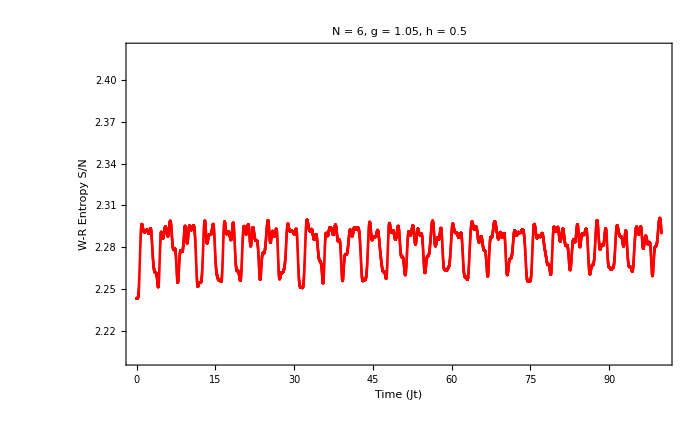

```mathematica
(*4. Plot with Correct Limits*)
ListPlot[evolutionData,PlotRange->{2.2,haarLimit},Frame->True,(*GridLines:Lower is always ln(3Pi),Upper is the calculated Haar limit*)GridLines->{{},{Log[3*Pi],haarLimit}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],ImageSize->700,PlotStyle->{Thickness[0.005],Red},PlotLabel->Style["N = "<>ToString[nSys]<>", g = "<>ToString[g]<>", h = "<>ToString[N[h]],25,Black]]
```

# improvement 2

```mathematica
(*0. Clear Everything& Start Kernels*)
ClearAll["Global`*"];
(*---2. HAMILTONIAN DEFINITION---*)
getHamiltonian[n_,g_,h_]:=Module[{sx=SparseArray[{{0,1},{1,0}}],sz=SparseArray[{{1,0},{0,-1}}],id=IdentityMatrix[2,SparseArray],H,op},
op[mat_,i_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,n],i->mat];
H=SparseArray[{},{2^n,2^n}];
Do[
H-=op[sz,i].op[sz,Mod[i,n]+1],{i,1,n}];
Do[H-=h*op[sx,i],{i,1,n}];
Do[H-=g*op[sz,i],{i,1,n}];
H];
```

```mathematica
(*---1. ROBUST PURITY FUNCTION (Must be defined on all kernels)---*)
getPuritySum[stateVec_,nSys_]:=Module[{puritySum=0,sub,mat,sv,dim=2^nSys,k,perm,tensor,tensorPerm},
Do[k=Length[sub];
If[k==0||k==nSys,puritySum+=1,(*Optimized Reshape/Permute*)
perm=Join[sub,Complement[Range[nSys],sub]];
tensor=ArrayReshape[stateVec,ConstantArray[2,nSys]];
tensorPerm=Transpose[tensor,perm];
mat=ArrayReshape[tensorPerm,{2^k,2^(nSys-k)}];
sv=SingularValueList[mat];
puritySum+=Total[Chop[sv]^4];];
,{sub,Subsets[Range[nSys]]}];
puritySum];
(*Distribute this function to all parallel kernels*)
DistributeDefinitions[getPuritySum];
```

```mathematica
(*---3. PARALLELIZED TIME EVOLUTION---*)
runParallelEvolution[nSys_,g_,h_,psi0_,tlist_]:=Module[{H,evals,evecs,c,dim=2^nSys,timeSteps,evolutionFunc},
Print["1. Constructing Hamiltonian (N=",nSys,")..."];
H=getHamiltonian[nSys,g,h];
Print["2. Diagonalizing (Master Kernel)..."];
(*We diagonalize once on the master kernel*)
{evals,evecs}=Eigensystem[N[H]];
(*Projection coefficients c_n= <n|psi0>*)
c=Conjugate[evecs].psi0;
(*3. PREPARE FOR PARALLELIZATION*)(*We need to send the large matrices (vectors/values) to the workers*)
Print["3. Distributing Data to Kernels..."];
DistributeDefinitions[evals,evecs,c,nSys];
(*Define the worker function that runs on each kernel*)(*It takes a time't',reconstructs the state,and computes entropy*)
evolutionFunc=Function[{t},Module[{psit,sumP,S},
(*Analytic Evolution:Reconstruct state vector at time t*)(*Transpose[evecs] turns rows back into column eigenvectors*)
psit=Transpose[evecs].(c*Exp[-I*evals*t]);
(*Heavy Calculation:SVDs of all subsystems*)
sumP=getPuritySum[psit,nSys];
(*Return Result {t,Entropy}*)
{t,Log[6*Pi]-Log[sumP]/nSys}]];
Print["4. Running Parallel Evolution..."];
(*PARALLEL MAP:This splits the timeSteps list across your 14 kernels*)
ParallelMap[evolutionFunc,tlist]];
```

```mathematica
(*---4. EXECUTE---*)
(*Parameters*)
Nval=8;
```

```mathematica
tlist=Table[10^i,{i,-1,12,0.0020}];
tlist//Length
```

6501

```mathematica
Print["Computing Haar limit for N=",Nval,"..."];
haarValues=Table[psi=Normalize[RandomComplex[{-1-I,1+I},2^Nval]];
sumP=getPuritySum[psi,Nval];
Log[6*Pi]-Log[sumP]/Nval,{20}];
haarLimit=Mean[haarValues];
Print["Haar Limit for N=",Nval," is ",haarLimit];
```

Computing Haar limit for N=8...

Haar Limit for N=8 is 2.44594

```mathematica
(*Initial State|00...0>*)
(*psi0=Normal[SparseArray[{1}->1,dim]];*)
(*psi0=RandomChainProductState[Nval];*)
(*psi0=Flatten[KroneckerProduct[haar[Nval/2],haar[Nval/2]]];*)
psi0=coherentstate[qubit[Pi/2,0],Nval];
```

```mathematica
g=2.0;
h=0.001;
```

```mathematica
(*Run*)
AbsoluteTiming[dataParallel=runParallelEvolution[Nval,g,h,psi0,tlist];]
```

1. Constructing Hamiltonian (N=8)...

2. Diagonalizing (Master Kernel)...

Eigensystem::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

3. Distributing Data to Kernels...

4. Running Parallel Evolution...

{7.30989,Null}

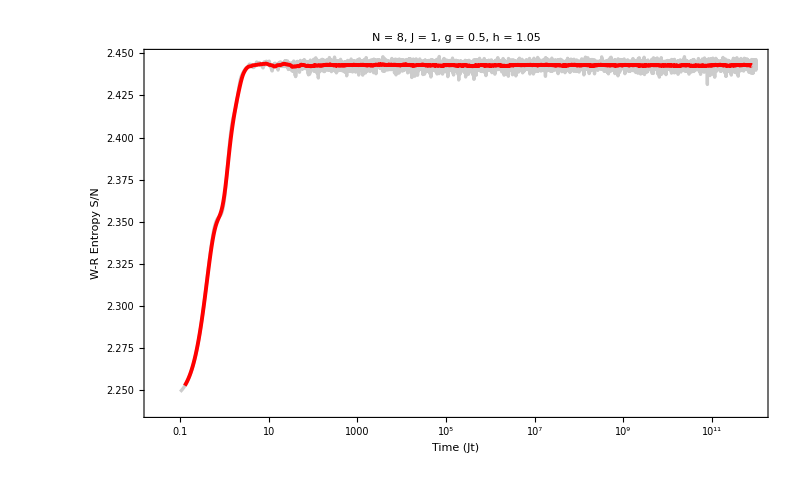

```mathematica
ListLogLinearPlot[{dataParallel,MovingAverage[dataParallel,100]},PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],haarLimit}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],ImageSize->800,PlotStyle->{{Thickness[0.003],Gray,Opacity[0.4]},{Thickness[0.0035],Red}},PlotLabel->Style["N = "<>ToString[Nval]<>", J = 1, g = "<>ToString[g]<>", h = "<>ToString[N[h]],25,Black],Joined->True,Background->White]
```

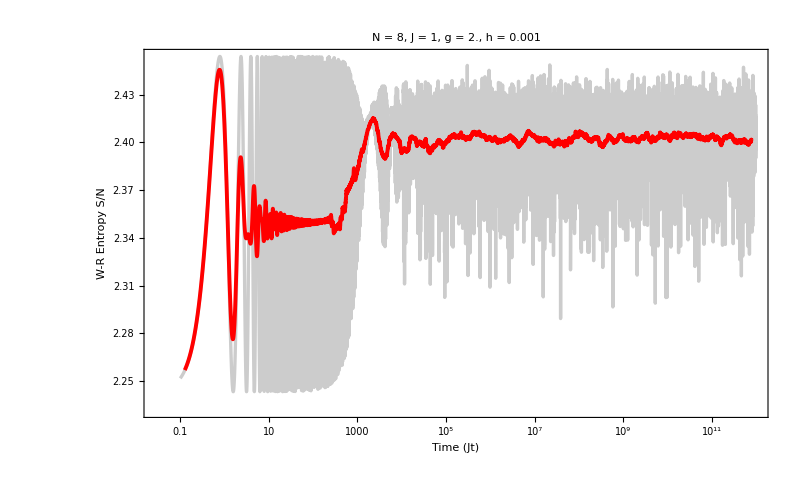

```mathematica
ListLogLinearPlot[{dataParallel,MovingAverage[dataParallel,100]},PlotRange->All,Frame->True,GridLines->{{},{Log[3*Pi],haarLimit}},GridLinesStyle->Directive[Dashed,Gray],FrameLabel->{"Time (Jt)","W-R Entropy S/N"},FrameStyle->Directive[Black,18],ImageSize->800,PlotStyle->{{Thickness[0.003],Gray,Opacity[0.4]},{Thickness[0.0035],Red}},PlotLabel->Style["N = "<>ToString[Nval]<>", J = 1, g = "<>ToString[g]<>", h = "<>ToString[N[h]],25,Black],Joined->True,Background->White]
```